# ODE

```mathematica
Solve [x^5-2*x+3==0,x]
```

{{x→Root[#1^5-2 #1+3&,1]},{x→Root[#1^5-2 #1+3&,2]},{x→Root[#1^5-2 #1+3&,3]},{x→Root[#1^5-2 #1+3&,4]},{x→Root[#1^5-2 #1+3&,5]}}

```mathematica
NSolve [x^5-2*x+3==0,x]
```

{{x→-1.42361},{x→-0.246729-1.32082 ⅈ},{x→-0.246729+1.32082 ⅈ},{x→0.958532-0.498428 ⅈ},{x→0.958532+0.498428 ⅈ}}

```mathematica
NSolve [x^5-2*x+3==0,x, Reals]
```

{{x→-1.42361}}

```mathematica
DSolve[psi'[x]==x,psi[x],x]
(* have to write independent variable as y[dependent variable] to indicate that y is a variable of the dependent variable *)
```

{{psi(x)→c_1+x^2/2}}

```mathematica
DSolve[psi''[x]+psi'[x]-6psi[x]==0,psi[x],x]
```

{{psi(x)→c_1 ⅇ^(-3 x)+c_2 ⅇ^(2 x)}}

#### Second Order Differential Equation with IC

```mathematica
soln=DSolve[{y''[x]+y'[x]-6y[x]==0,y[0]==3,y'[0]==1},y[x],x]
```

{{y(x)→ⅇ^(-3 x) (2 ⅇ^(5 x)+1)}}

```mathematica
{{y(x)->ⅇ^(-3 x) (2 ⅇ^(5 x)+1)}}
```

```mathematica
ClearAll[psi]
Clear[psi''[x]]
DSolve[{psi''[x]+psi'[x]-6psi[x]==0,psi[0]==3,psi'[0]==1},psi[x],x]
```

Clear::ssym: TraditionalForm` is not a symbol or a string.

DSolve::deqn: Equation or list of equations expected instead of TraditionalForm`True in the first argument TraditionalForm`.

DSolve[{psi''(x)+psi'(x)-6 psi(x)==0,psi(0)==3,True},psi(x),x]

#### Replace All(giving input in a function)

```mathematica
x^3+2x-1/.x -> 3
```

32

#### Function Input

```mathematica
f[x_]=x^3+2x-1
f[3]
```

x^3+2 x-1

32

#### Plotting Differential Equation Solution

```mathematica
y[x]/.soln[[1]]
(* Retrieving Solution *)
```

ⅇ^(-3 x) (2 ⅇ^(5 x)+1)

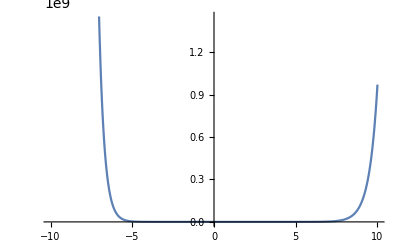

```mathematica
Plot[%,{x,-10,10}]
```

#### Exercise: Plotting the solutions of second order differential equation for constants (C2,C2)=(2,3),(4,5),(6,7)

```mathematica
sol=DSolve[y''[x]+4y[x]==7,y[x],x]
```

{{y(x)→c_2 sin(2 x)+c_1 cos(2 x)+7/4}}

```mathematica
y[x]/.sol[[1]]
```

c_2 sin(2 x)+c_1 cos(2 x)+7/4

```mathematica
Tofsol= Table[y[x]/.sol/.{C[1]->k1, C[2] ->   k2}, {k1,2,3}, {k2,4,6}];
```

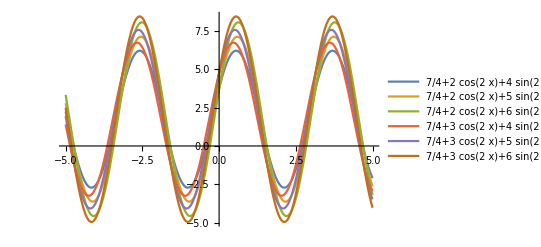

```mathematica
Plot[Tofsol, {x,-5,5}, PlotLegends -> "Expressions"]
```